{1/2 ⅇ^(2 ⅈ k L) (2 Cos[2 √(d+k^2) L]-(ⅈ (d+2 k^2) Sin[2 √(d+k^2) L])/(k √(d+k^2)))}

{2 k √(d-k^2) Cos[2 √(d-k^2) L]-(d-2 k^2) Sin[2 √(d-k^2) L]}

{1-(ⅈ α)/(2 k)}

-(L x √(4 d-x^2/L^2))/(2 d L^2-x^2)

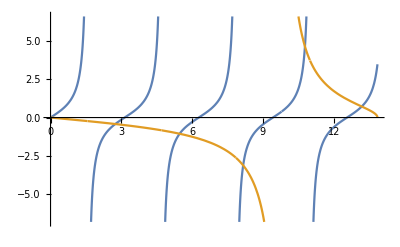

```mathematica
s = Solve[c1*I*Sqrt[d+k*k]*Exp[-I*Sqrt[d+k*k]*L]-c2*I*Sqrt[d+k*k]*Exp[I*Sqrt[d+k*k]*L]==-I*k*Exp[I*k*L] && c1*Exp[-I*Sqrt[d+k*k]*L]+c2*Exp[I*Sqrt[d+k*k]*L]==Exp[I*k*L],{c1,c2}];
c1=s[[All,1,2]];
c2=s[[All,2,2]];
t = Solve[c3*(I*k)*Exp[I*k*L]-c4*(I*k)*Exp[-I*k*L]==c1*I*Sqrt[d+k*k]*Exp[I*Sqrt[d+k*k]*L]-c2*I*Sqrt[d+k*k]*Exp[-I*Sqrt[d+k*k]*L]&& c3*Exp[I*k*L]+c4*Exp[-I*k*L]==c1*Exp[I*Sqrt[d+k*k]*L]+c2*Exp[-I*Sqrt[d+k*k]*L],{c3,c4}];
c3=Together[FullSimplify[t[[All,1,2]]]];
c4[k_]=Together[FullSimplify[t[[All,2,2]]]];

ss = Solve[b1*I*Sqrt[d+k*k]*Exp[I*Sqrt[d+k*k]*L]-b2*I*Sqrt[d+k*k]*Exp[-I*Sqrt[d+k*k]*L]==I*k*Exp[I*k*L] && b1*Exp[I*Sqrt[d+k*k]*L]+b2*Exp[-I*Sqrt[d+k*k]*L]==Exp[I*k*L],{b1,b2}];
b1=ss[[All,1,2]];
b2=ss[[All,2,2]];
tt = Solve[b3*(I*k)*Exp[-I*k*L]-b4*(I*k)*Exp[I*k*L]==b1*I*Sqrt[d+k*k]*Exp[-I*Sqrt[d+k*k]*L]-b2*I*Sqrt[d+k*k]*Exp[I*Sqrt[d+k*k]*L]&& b3*Exp[-I*k*L]+b4*Exp[I*k*L]==b1*Exp[-I*Sqrt[d+k*k]*L]+b2*Exp[I*Sqrt[d+k*k]*L],{b3,b4}];
b3[d_]=Together[FullSimplify[tt[[All,1,2]]]];
b4=tt[[All,2,2]];

FullSimplify[c4[k]];
FullSimplify[b3[d]];
FullSimplify[Sqrt[d+k*k]/k*(b1*c2-b2*c1)]

aknum= Simplify[Numerator[c4[I*k]]]

Limit[b3[α/(2*L)],L->0]


Rightfunc[x_] = Simplify[x/L*Sqrt[d-(x/(2*L))*(x/(2*L))]/(-d+(x/L)*(x/L)/2)]
d = 3;
L = 4;
Plot[{Tan[x],x/L*Sqrt[d-(x/(2*L))*(x/(2*L))]/(-d+(x/L)*(x/L)/2)},{x,0,2*Sqrt[d*L*L]}]
```